## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="FBA1";
fitLabel="";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_FBA1_test";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/FBA1/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{{{fdp,Null}},Keq substrate}

{0.00016,Keq value}

{fdp,Km or S05 substrate}

{0.00002,Km or S05 value}

{{{fdp,Null}},kcat substrates}

{0.217,kcat value}

{fdp,Km or S05 substrate}

{0.00002,Km or S05 value}

{{{fdp,Null},{cit,0.011}},kcat substrates}

{3.17,kcat value}

{fdp,Km or S05 substrate}

{0.00007,Km or S05 value}

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 8-10

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00002 | 0.000019
0.000021 |  | M | 7.5 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.412114 | 0.39882
0.423509 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null
cit | 0.011 | 6.02029 | 5.71642
6.32415 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {0,2,1};
s05Priorities = Null;
kcatPriorities = {10,10};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 8-10

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
2 | fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | fdp | Null | 0.412114 | 0.39882
0.423509 | 1/s | 8 | 37 | trishcl | 0.05 | 
10 | fdp | Null
cit | 0.011 | 6.02029 | 5.71642
6.32415 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

```mathematica
catalyticBranch={"E_FBA1[c] + fdp[c] <=> E_FBA1[c]&fdp",
				"E_FBA1[c]&fdp <=> E_FBA1[c]&dhap&g3p",
				"E_FBA1[c]&dhap&g3p <=> E_FBA1[c]&dhap + g3p[c]",
				"E_FBA1[c]&dhap <=> E_FBA1[c] + dhap[c]",
				
				"E_FBA1[c] + cit[c] <=> E_FBA1[c]&cit",
				"E_FBA1[c]&cit + fdp[c] <=> E_FBA1[c]&cit&fdp",
				"E_FBA1[c]&cit&fdp <=> E_FBA1[c]&cit&dhap&g3p",
				"E_FBA1[c]&cit&dhap&g3p <=> E_FBA1[c]&cit&dhap + g3p[c]",
				"E_FBA1[c]&cit&dhap <=> E_FBA1[c]&cit + dhap[c]"};


enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((FBA1^c)_^+cit^c⇌(FBA1^c&cit^c)_^)^FBA11,((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA12,((FBA1^c&cit^c)_^+fdp^c⇌(FBA1^c&cit^c&fdp^c)_^)^FBA13,((FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c)^FBA14,((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA15,((FBA1^c&cit^c&dhap^c)_^⇌(FBA1^c&cit^c)_^+dhap^c)^FBA16,((FBA1^c&cit^c&fdp^c)_^⇌(FBA1^c&cit^c&dhap^c&g3p^c)_^)^FBA17,((FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c)^FBA18,((FBA1^c&cit^c&dhap^c&g3p^c)_^⇌(FBA1^c&cit^c&dhap^c)_^+g3p^c)^FBA19}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA12,Overscript[(FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c, FBA14],((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA15,Overscript[(FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c, FBA19]};
catalyticReactionsSet2={((FBA1^c&cit^c)_^+fdp^c⇌(FBA1^c&cit^c&fdp^c)_^)^FBA13,Overscript[(FBA1^c&cit^c&dhap^c)_^⇌(FBA1^c&cit^c)_^+dhap^c, FBA16],((FBA1^c&cit^c&fdp^c)_^⇌(FBA1^c&cit^c&dhap^c&g3p^c)_^)^FBA17,Overscript[(FBA1^c&cit^c&dhap^c&g3p^c)_^⇌(FBA1^c&cit^c&dhap^c)_^+g3p^c, FBA19]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites,assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((FBA1^c&fdp^c)_^-((FBA1^c&dhap^c&g3p^c)_^)/K_FBA15) Volume_c k_FBA15^⟶,((FBA1^c&cit^c&fdp^c)_^-((FBA1^c&cit^c&dhap^c&g3p^c)_^)/K_FBA17) Volume_c k_FBA17^⟶}

Volume_c (-(FBA1^c&dhap^c&g3p^c)_^ k_FBA15^⟵+(FBA1^c&fdp^c)_^ k_FBA15^⟶-(FBA1^c&cit^c&dhap^c&g3p^c)_^ k_FBA17^⟵+(FBA1^c&cit^c&fdp^c)_^ k_FBA17^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	cit[c]	param_FBA1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00016
2	0	2.0000000000000003e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.09090909090909091
2	0	3.1697863849222286e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.13680688860321005
2	0	5.023772863019165e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.20076000891310186
2	0	7.96214341106994e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.2847472489508013
2	0	0.000012619146889603861	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.3868631798468569
2	0	0.00002	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.49999999999999994
2	0	0.00003169786384922229	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.6131368201531432
2	0	0.00005023772863019165	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.7152527510491988
2	0	0.00007962143411069939	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.7992399910868981
2	0	0.0001261914688960386	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.86319311139679
2	0	0.00020000000000000004	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	7.000000000000002e-6	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.000011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.13680688860321008
1	0	0.00001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.000027867501938744792	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.2847472489508013
1	0	0.000044167014113613516	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.3868631798468569
1	0	0.00007000000000000002	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.00011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.7152527510491989
1	0	0.0002786750193874482	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.7992399910868984
1	0	0.0004416701411361352	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0007000000000000001	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.9090909090909092
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.41211435266581287
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.020288008989064

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	dhap[c]	fdp[c]	g3p[c]	cit[c]	param_FBA1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_2.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/haldaneRatio_3.txt"	0.00015593331597644444
2	0	1.6812207033805242e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.09090909090909086
2	0	2.6645552478124785e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.13680688860321
2	0	4.223035473194534e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.20076000891310175
2	0	6.693060172987803e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.2847472489508011
2	0	0.000010607785504900977	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.3868631798468567
2	0	0.00001681220703380524	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.49999999999999983
2	0	0.000026645552478124786	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.6131368201531431
2	0	0.00004223035473194534	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.7152527510491986
2	0	0.00006693060172987804	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.799239991086898
2	0	0.00010607785504900977	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.8631931113967898
2	0	0.0001681220703380524	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	0.000010213623145305739	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.09090909090909081
1	0	0.000016187501793358336	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.1368068886032099
1	0	0.000025655461395245704	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.20076000891310167
1	0	0.000040661166114773754	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.284747248950801
1	0	0.00006444360537283544	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.38686317984685653
1	0	0.00010213623145305738	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.49999999999999967
1	0	0.00016187501793358337	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.6131368201531429
1	0	0.00025655461395245705	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.7152527510491985
1	0	0.00040661166114773793	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.7992399910868981
1	0	0.0006444360537283544	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.8631931113967898
1	0	0.0010213623145305737	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/relRateFor_fdp.txt"	0.909090909090909
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	0.39860256243229675
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014
10	0	1	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1_test/input/absRateFor.txt"	6.051940079508014

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};


{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
numCPUs =1;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel, numCPUs];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 746.633696429
best_fit: 1.04373349487
best_fit: 1.07313529174
best_fit: 746.625936523
best_fit: 746.633023342

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 1.10756×10^-11 | 1.22669×10^-22 | 4.0805×10^-15 | 2.55031×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 6.0747×10^-12 | 3.69019×10^-23 | 2.23809×10^-15 | 1.39881×10^-9 | 0.00016 | 0.00016
2 | relRateFor_fdp | 3.22501×10^-6 | 1.04007×10^-11 | 6.75075×10^-7 | 0.000742583 | 0.0909091 | 0.0909084
2 | relRateFor_fdp | 2.62366×10^-6 | 6.88357×10^-12 | 8.26474×10^-7 | 0.000604117 | 0.136807 | 0.136806
2 | relRateFor_fdp | 1.78574×10^-6 | 3.18887×10^-12 | 8.25487×10^-7 | 0.000411181 | 0.20076 | 0.200759
2 | relRateFor_fdp | 6.85334×10^-7 | 4.69682×10^-13 | 4.49342×10^-7 | 0.000157804 | 0.284747 | 0.284747
2 | relRateFor_fdp | 6.52599×10^-7 | 4.25886×10^-13 | 5.81326×10^-7 | 0.000150267 | 0.386863 | 0.386864
2 | relRateFor_fdp | 2.13493×10^-6 | 4.55794×10^-12 | 2.45794×10^-6 | 0.000491588 | 0.5 | 0.500002
2 | relRateFor_fdp | 3.61727×10^-6 | 1.30847×10^-11 | 5.10689×10^-6 | 0.000832911 | 0.613137 | 0.613142
2 | relRateFor_fdp | 4.95522×10^-6 | 2.45542×10^-11 | 8.16095×10^-6 | 0.00114099 | 0.715253 | 0.715261
2 | relRateFor_fdp | 6.05564×10^-6 | 3.66708×10^-11 | 0.0000111444 | 0.00139437 | 0.79924 | 0.799251
2 | relRateFor_fdp | 6.89358×10^-6 | 4.75214×10^-11 | 0.0000137016 | 0.00158732 | 0.863193 | 0.863207
2 | relRateFor_fdp | 7.49494×10^-6 | 5.61742×10^-11 | 0.000015689 | 0.00172579 | 0.909091 | 0.909107
1 | relRateFor_fdp | 0.0000112863 | 1.27381×10^-10 | 2.36249×10^-6 | 0.00259874 | 0.0909091 | 0.0909067
1 | relRateFor_fdp | 9.18165×10^-6 | 8.43027×10^-11 | 2.89228×10^-6 | 0.00211413 | 0.136807 | 0.136804
1 | relRateFor_fdp | 6.249×10^-6 | 3.905×10^-11 | 2.88869×10^-6 | 0.00143888 | 0.20076 | 0.200757
1 | relRateFor_fdp | 2.39764×10^-6 | 5.74867×10^-12 | 1.57202×10^-6 | 0.000552075 | 0.284747 | 0.284746
1 | relRateFor_fdp | 2.28509×10^-6 | 5.22164×10^-12 | 2.03553×10^-6 | 0.000526163 | 0.386863 | 0.386865
1 | relRateFor_fdp | 7.47326×10^-6 | 5.58497×10^-11 | 8.60399×10^-6 | 0.0017208 | 0.5 | 0.500009
1 | relRateFor_fdp | 0.0000126615 | 1.60314×10^-10 | 0.0000178758 | 0.00291546 | 0.613137 | 0.613155
1 | relRateFor_fdp | 0.0000173444 | 3.00828×10^-10 | 0.0000285656 | 0.00399377 | 0.715253 | 0.715281
1 | relRateFor_fdp | 0.000021196 | 4.49269×10^-10 | 0.0000390083 | 0.00488067 | 0.79924 | 0.799279
1 | relRateFor_fdp | 0.0000241288 | 5.822×10^-10 | 0.0000479592 | 0.00555602 | 0.863193 | 0.863241
1 | relRateFor_fdp | 0.0000262337 | 6.88205×10^-10 | 0.0000549155 | 0.00604071 | 0.909091 | 0.909146
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 2.32755×10^-11 | 5.41749×10^-22 | 2.20868×10^-11 | 5.35938×10^-9 | 0.412114 | 0.412114
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029
10 | absRateFor | 1.56363×10^-11 | 2.44493×10^-22 | 2.16754×10^-10 | 3.60039×10^-9 | 6.02029 | 6.02029

### Simulated Data and Best Fit Data Plot

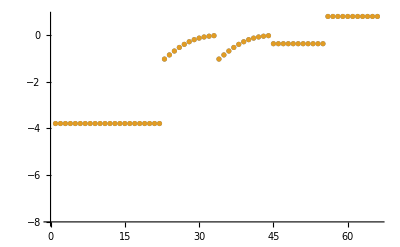

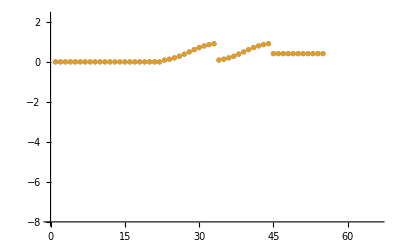

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

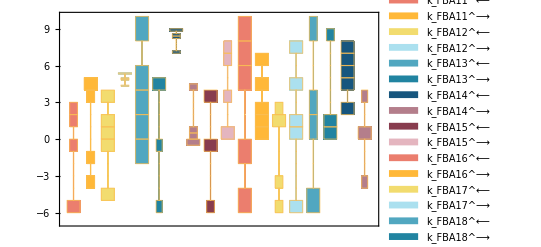

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

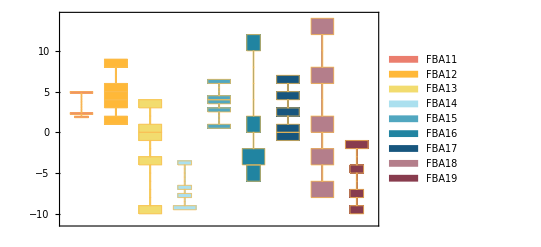

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

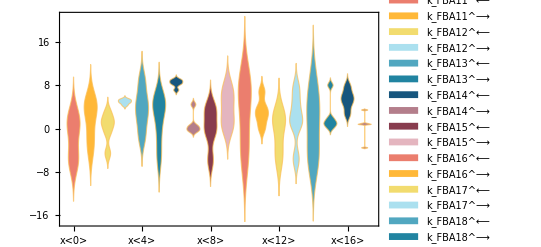

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

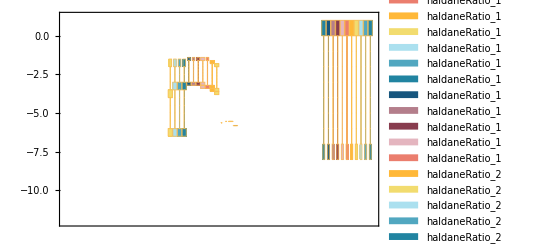

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet =1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00002 | 0.0000199998 | 0.000983151
0.00007 | 0.0000699976 | 0.00344129

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
0.412114 | 0.4113 | 0.197611
6.02029 | 5.97885 | 0.688255

```mathematica
backCalculateRatios[haldaneRatiosList, {KeqList[[1]][[3]],KeqList[[1]][[3]]}, paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016
0.00016 | 0.00016
0.00016 | 2.55031×10^-9
1.39881×10^-9

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

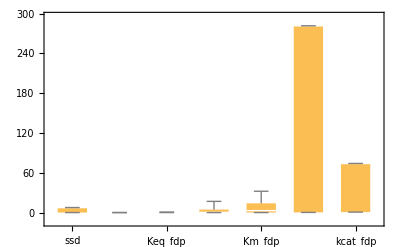

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```